# H(z) data on dark energy parameterisations.

## Created by C. Escamilla-Rivera. March 2017

You are free to use, distribute, and modify this code, as long as you cite the respective papers/references:
(I) Cosmological constraints combining H(z), CMB shift and SNIa observational data. JCAP 0707 (2007) 015
(II) Status on bidimensional dark energy parameterizations using SNe Ia JLA and BAO datasets. Galaxies 4 (2016) 8

Can I modify the code? 
Yes, you can. In fact, I actively encourage it! It would be great if you could release any modifications that you make to the code, so that they can be shared by everyone. I’m not a stickler about it, though, as long as: (a) you’re nice about it, (b) make good faith attempts to describe and/or share your modifications if asked, and (c) you give proper credit.

But please do email me if you get stuck: cescamilla@mctp.mx

```mathematica
(*Terminate/Restart Mathematica kernel session*)
Quit[];
```

```mathematica
(*Calling Mathematica packages*)
Needs["ErrorBarPlots`"]
```

```mathematica
(*Calling datasets. In this case, the H(z) data from Reference I. Each vector contains the following in each column: {z,H,Subscript[σ, z]}*)
dataH={{0.0,72,8},{0.1,69,12},{0.17,83,8},{0.27,77,14},{0.4,95,17},{0.48,97,60},{0.88,90,40},{0.9,117,23},{1.3,168,17},{1.43,177,18},{1.53,140,14},{1.75,202,40}};
```

```mathematica
(*Taking each data frome each column from dataH*)
zlist=dataH[[All,1]]
Hlist=dataH[[All,2]]
sigmalist=dataH[[All,3]]
```

{0.,0.1,0.17,0.27,0.4,0.48,0.88,0.9,1.3,1.43,1.53,1.75}

{72,69,83,77,95,97,90,117,168,177,140,202}

{8,12,8,14,17,60,40,23,17,18,14,40}

```mathematica
(*Exploring dark energy parameterisation. Example: CPL parameterisation*)
expde[z_,w0_,w1_]:=(1+z)^(3(1+w0+w1))*Exp[-3w1* z/(1+z)];
Efun[z_?NumericQ,om_?NumericQ,c1_?NumericQ,c2_?NumericQ]:=Sqrt[om (1+z)^3+(1-om)*expde[z,c1,c2]]
```

```mathematica
(*Friedmann/Evolution equation*)
Hth[z_,om_,w0_,w1_]:=Sqrt[om (1+z)^3+(1-om)*expde[z,w0,w1]]
```

```mathematica
(*Statistical χ^2*)
chisq[om_,w0_,w1_]:=If[0.0≤ om ≤ 0.6 && -5.5≤ w0≤ 5.33 && -10.0≤ w1 ≤ 10.0 ,Total[(72.4Hth[zlist,om,w0,w1] - Hlist)^2/sigmalist^2],$MaxNumber/2.]
```

```mathematica
(*Test*)
chisq[0.24,-1.08, 0.058]
```

9.45112

```mathematica
(*Switches off a message: reason "not converge to the tolerance"*)
Off[FindMinimum::"eit"];
```

```mathematica
om=0.1338/0.742^2;
```

```mathematica
fm=FindMinimum[{chisq[0.243, w0, w1], -1.5≤ w0≤ -0.333 && -5.0≤ w1 ≤ 5.0},{w0, w1}]
```

{7.51258,{w0→-0.820913,w1→-0.0210058}}

```mathematica
bestfit1=fm[[1]];
```

```mathematica
(*Note: 3-sigma rule theory*)
(1-Gamma[1,2.30/2]/Gamma[1])*100
(1-Gamma[1,6.28/2]/Gamma[1])*100
(1-Gamma[1,11.83/2]/Gamma[1])*100
(1-Gamma[1,19.33/2]/Gamma[1])*100
```

68.3363

95.6717

99.7301

99.9937

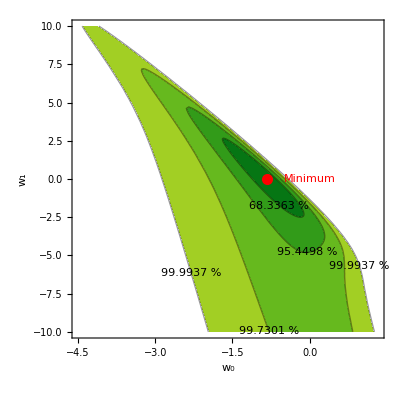

```mathematica
PlotCPL=ContourPlot[chisq[om, w0,w1] -bestfit1,{w0, -4.5, 1.33},{w1, -10.0, 10.0 }, Contours->{2.30,6.18,11.83,19.33},ContourLabels->(Text[(1-Gamma[1,#3/2]/Gamma[1])*100 "%",{#1,#2}]&),ContourShading->{ColorData["AvocadoColors"][0.27],ColorData["AvocadoColors"][0.42],ColorData["AvocadoColors"][0.57],ColorData["AvocadoColors"][0.72],White},PlotPoints->20,FrameLabel->{"w_0","w_1"},LabelStyle->{18},ImageSize->{400,400}, Epilog-> {Red, PointSize[0.02],Text["Minimum"], Point[{fm[[2]][[1]][[2]], fm[[2]][[2]][[2]]}]}]
```

# Task 1: Explore LC/Wang parametrisation

Compute the χ^2-statistics, best fit values (w_0,w_0.5) and report the confidence contours. Check the differences.